```mathematica
a*a*a*b*b*c
```

a^3 b^2 c

```mathematica
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s + n
```

n+Zeta[s]

```mathematica
1+2
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,1,{3,4,5},{3,2}}
```

{1,1,{3,4,5},{3,2}}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]] (*print the number of sin2*)
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]](*doesnt start from 0 like python*)
```

9

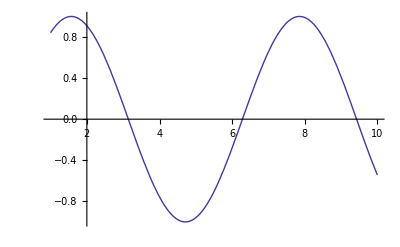

```mathematica
Plot[Sin[x],{x,1,10}]
```

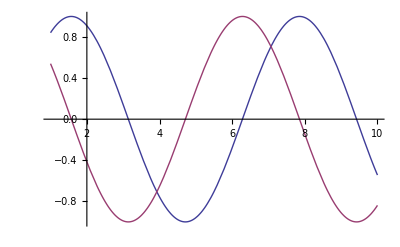

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
3 x-x+2(*begin Question 3*)
```

2+2 x

```mathematica
x^2+x-4 x^2 (*mathematica knows order of operations*)
```

x-3 x^2

```mathematica
(x+2 y+1) (x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
Expand[%] (*Expand[expr]    multiply out products and powers,writing the result as a sum of terms*)
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%] (*Factor[expr] write expr as a product of minimal factors*)
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
1+2 x/.x->3 (*expr/.x->value   replace x by value in the expression expr*)
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a} (*expr/.{x->xval,y->yval} perform several replacements*)
```

(4-a) (2+a)^2

```mathematica
x=1+a
```

1+a

```mathematica
x+5-2 x
```

6+a-2 (1+a)

```mathematica
x=. (*putting =. erases value of x*)
```

```mathematica
x+5-2 x
```

5-x

```mathematica
Simplify[x^2+2 x+1] (*Simplify[expr] try to find the simplest form of expr by applying various standard algebraic transformations*)
```

(1+x)^2

```mathematica
D[x^n,x](*begin Question 4*)(*D[f,x] partial derivative of  f with respect to x*)
```

n x^(-1+n)

```mathematica
D[x^n,{x,3}](*gives 3rd derivative*)
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x[1]^2+x[2]^2,x[1]](*with respect to x[1]*)
```

2 x[1]

```mathematica
D[x^2+y[x]^2,x](*says y is in terms of x*)
```

2 x+2 y[x] y'[x]

```mathematica
D[x^2+y^2,{{x,y}}](*D[f,{{x1,x2,...}}] the gradient of a scalar function*)
```

{2 x,2 y}

```mathematica
Integrate[x^n,x](*Integrate[f,x] the indefinite integral*)
```

x^(1+n)/(1+n)

```mathematica
Integrate[Sin[x]^2,{x,a,b}](*a and b  are the limits of the integral*)
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x](*DSolve[eqn,y[x],x] solve a differential equation for y[x]*)
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==1/(x1 x2),y[x1,x2],{x1,x2}]
```

{{y[x1,x2]→(-Log[x1]+Log[x2]+x1 C[1][-x1+x2]-x2 C[1][-x1+x2])/(x1-x2)}}

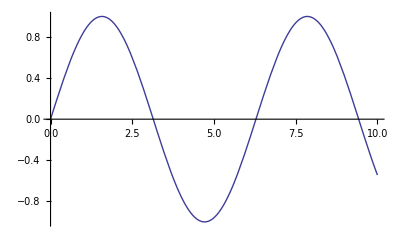

```mathematica
Plot[Sin[x],{x,0,10}](*start Question 5*)
```

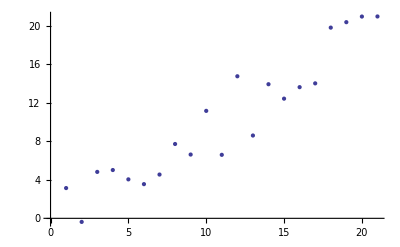

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

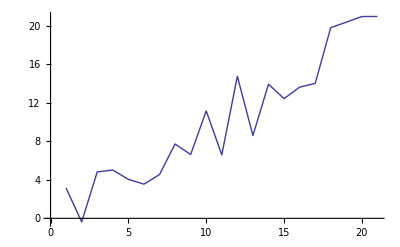

```mathematica
ListLinePlot[datapts]
```

```mathematica
GraphicsGrid[{{Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}],Plot3D[Sin[x]*Cos[y],{x,0,5},{y,1,10},ColorFunction->(Hue[#3]&),MeshFunctions->(#3&),Boxed->False,Axes->False]}}]
```

-Graphics-

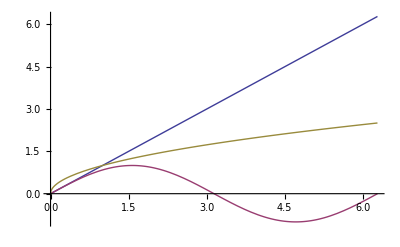

```mathematica
Plot[{x,Sin[x],Sqrt[x]},{x,0,2 Pi}]
```

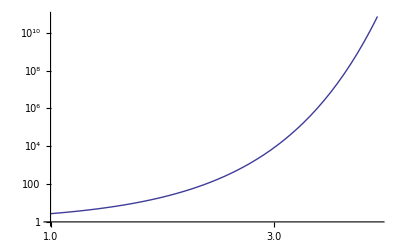

```mathematica
LogLogPlot[E^x^2,{x,1,5}](*plots both axises on log scale. LogPlot is y axis log scale and LogLinearPlot is on x axis*)
```

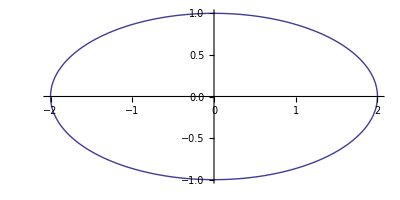

```mathematica
ParametricPlot[{2 Sin[t],Cos[t]},{t,0,2 Pi}]
```

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

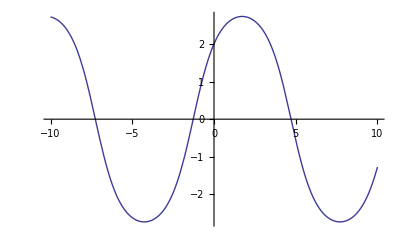

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
sol=NDSolve[ode1,y,{x,-10,10}]
Plot[y[x]/.sol,{x,-10,10}]
```

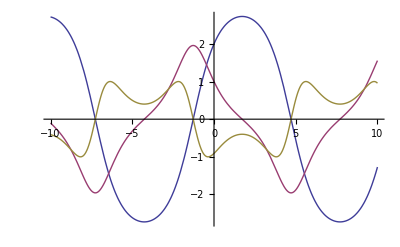

```mathematica
Plot[Evaluate[{y[x],y'[x],y''[x]}/.sol],{x,-10,10}](*plots with derivatives, the evaluate makes the graphs different colors*)
```

```mathematica
Manipulate[Module[{sol=NDSolve[{y''[x]+Sin[y[x]]==0,y[0]==p[[1]],y'[0]==p[[2]]},y,{x,0,T}]},ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,0,T},PlotRange->{{-4,4},{-3,3}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}](*apperance lets you see the n value*)
```

```mathematica
Manipulate[Plot[a1 Sin[n1 (x+p1)]+a2 Sin[n2 (x+p2)],{x,0,2 Pi},PlotRange->2],{n1,1,20},{a1,0,1},{p1,0,2 Pi},{n2,1,20},{a2,0,1},{p2,0,2 Pi}](*manipulate can also take more than one varible*)
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20}]
```

```mathematica
Manipulate[n,{n,1,20,1}](*the extra 1 at the end is for step size*)
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],{n,1/2,1/3,1/144},{m,1/2,1/3,1/144}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{a1,0,1},{p1,0,2 Pi},{n2,1,4},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{{a1,1},0,1},{p1,0,2 Pi},{{n2,5/4},1,4},{{a2,1},0,1},{p2,0,2 Pi}](*this is the same as the previous graph excpet the varibales have intial values*)
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{n2,5/4,"Frequency 2"},1,4},Delimiter,{{a1,1,"Amplitude 1"},0,1},{{a2,1,"Amplitude 2"},0,1},Delimiter,{{p1,0,"Phase 1"},0,2 Pi},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],"Horizontal",{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,"Vertical",{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```